```mathematica
f[a_,b_,k1_,k2_,k3_]:= k1*a*a*b+k2-k3*a
```

```mathematica
g[a_,b_,k1_,k2_,k4_]:= -k1*a*a*b+k4
```

```mathematica
{k1=0.0004, k2=50, k3=10, k4=100}
```

{0.0004,50,10,100}

```mathematica
{aBar = (k2+k4)/k3,bBar = k4/(k1*aBar^2)}
```

{15,1111.11}

```mathematica
J={{2*k1*aBar*bBar-k3,k1*aBar^2},{-2*k1*aBar*bBar,-k1*aBar}}
```

{{3.33333,0.09},{-13.3333,-0.006}}

```mathematica
Eigenvalues[J]
```

{2.92374,0.403593}

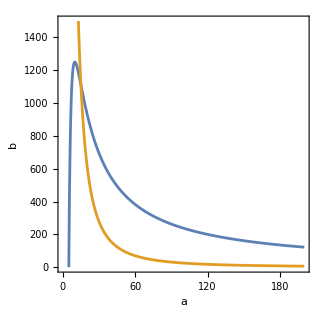

```mathematica
p1 = ContourPlot[{f[a,b,k1,k2,k3]==0,g[a,b,k1,k2,k4]==0},{a,0,200},{b,0,1500},PlotPoints->200,FrameLabel->{a,b}]
```

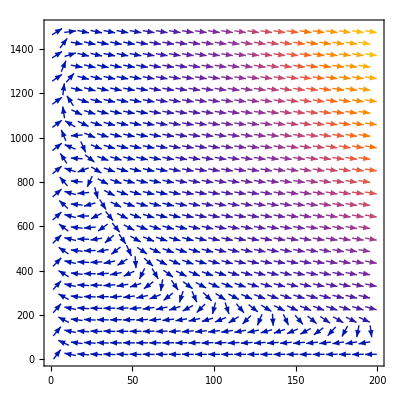

```mathematica
p2 = VectorPlot[{f[a,b,k1,k2,k3],g[a,b,k1,k2,k4]},{a,0,200},{b,0,1500},VectorPoints->Fine]
```

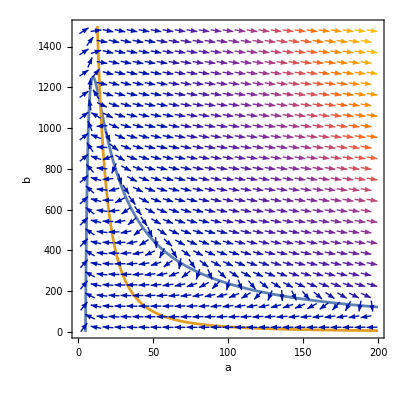

```mathematica
Show[p1,p2]
```